```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Linear Filters

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Three common “kinds” of functions in image processing are filters, spatial mappings, and transforms. Filters change the value of the pixels based on the values of all the pixels in a local neighborhood, spatial mappings leave the values of the pixels intact (more or less) but move them from one spatial location to another, and transforms calculate the value of each output pixel using the complete image. An important choice in filters is the size of the local neighborhood.

```mathematica
TableForm[{{Hyperlink["Filter1D",{"visualVocabFilters.nb","labelFilter1D"}],labelFilter1D},{Hyperlink["FreqSelect",{"visualVocabFilters.nb","labelFreqSelect"}],labelFreqSelect},{Hyperlink["Neighborhood",{"visualVocabFilters.nb","labelNeighborhood"}],labelNeighborhood},{Hyperlink["FilterSynth",{"visualVocabFilters.nb","labelFilterSynth"}],labelFilterSynth},{Hyperlink["FilterXRay",{"visualVocabFilters.nb","labelFilterXRay"}],labelFilterXRay},{Hyperlink["FilterColor",{"visualVocabFilters.nb","labelFilterColor"}],labelFilterColor},{Hyperlink["HighPassXRay",{"visualVocabFilters.nb","labelHighPassXRay"}],labelHighPassXRay},{Hyperlink["GradientXRay",{"visualVocabFilters.nb","labelGradientXRay"}],labelGradientXRay},{Hyperlink["EdgeFilter",{"visualVocabFilters.nb","labelEdgeFilter"}],labelEdgeFilter},{Hyperlink["EdgeFilterColor",{"visualVocabFilters.nb","labelEdgeFilterColor"}],labelEdgeFilterColor},{Hyperlink["BuiltInFilters",{"visualVocabFilters.nb","labelBuiltInFilters"}],labelBuiltInFilters},{Hyperlink["Sharpen",{"visualVocabFilters.nb","labelSharpen"}],labelSharpen}}]
```

| Calculating the convolution
 | Frequency selective filters can remove unwanted portions of a signal based on the frequency content
 | Common shapes for the impulse response of a filter
 | Filtering synthetic images with various neighborhoods
 | Filtering x-ray images with various neighborhoods
 | Combining different neightborhoods with subtraction
 | Filtering x-ray tiles with the Sobel highpass filter
 | The gradient filter is another variety of highpass filter
 | When the gradient filter is applied to color images,
it is actually applied to a grayscale version
 | The LaplacianGaussianFilter[ ] is applied separately to
the red, green and blue channels
 | Mathematica has a number of built-in filter types
 | The sharpen filter does a nice job emphasizing the cracks in the canvas

Important commands in this notebook include ListConvolve[ ], which carries out the convolution of two sequences (i.e., the filtering of one sequence by another) and ImageConvolve[ ], which carries out the convolution of an image and a specified kernel.

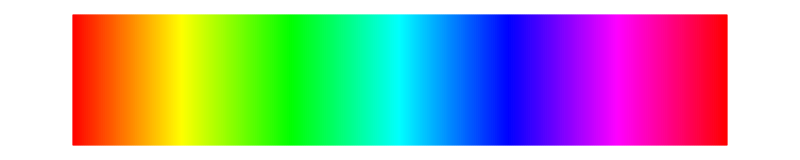

```mathematica
specLine
```

Say there is a sequence of data that has an undesirable property: maybe it has too much high frequency noise, or maybe there is a low frequency trend, or maybe there is only a small range of frequencies where all the useful stuff happens (or conversely, maybe there is a range of frequencies where only bad stuff happens). The problem can often be fixed by filtering, which is diagrammed in the figure below. A sequence of numbers is highlighted in green and a filter kernel (which can be designed to attenuate or augment certain frequency ranges within the signal) is shown in yellow. Combining the yellow numbers with the green numbers in a patterned way leads to the blue output sequence: with luck (and careful design) this output sequence has all the desirable properties of the green sequence without the undesirable properties.

```mathematica
Column[{Image[-Graphics-,ImageSize->800] ,Style["Filtering uses a kernel w (yellow) to process a data sequence (green) in a pattern called convolution; the output is a new sequence (blue).",captionStyle]},Alignment->Center](* 1dimFiltering.ai *)
```

-Graphics-
Filtering uses a kernel w (yellow) to process a data sequence (green) in a pattern called convolution; the output is a new sequence (blue).

### One-Dimensional Linear Filters

The simplest filters, point filters, use a local neighborhood of size one (i.e., just the pixel value itself), and are limited in what they can accomplish. Once the neighborhood is enlarged to contain more points, the possibilities expand rapidly. For example, a neighborhood-three filter (as shown below in yellow in impulse responses 1 and 2) is defined by 3 numbers labeled w[1], w[2], and w[3]. The filtering process at a point k in the green data sequence f consists of combining w[1] with f[k+2], w[2] with f[k+1], and w[3] with f[k] for all k, in this case, for k between 1 and 32. These three combinations are then fused together to give a single number, which is the value g[k+2] that the output assumes at the point k+2. The filter then moves on to the next location, repeating the procedure for every point in the data. The output of the filtering is shown in blue. Depending on exactly how the pairs are combined and fused, the filter may be classified as linear (as below, and discussed throughout this section) or nonlinear.

```mathematica
labelFilter1D="Calculating the convolution";
infoFilter1D="The inner workings of five linear filters\n\nImpulse response 1 sums every triplet of data in the input. Why are there only four different values in the output sequence g[k]?\n\nImpulse response 2 takes the central value of each triplet and subtracts off (weighted versions of) its two neighbors. Explain why this suppresses low frequencies.\n\nWhat kind of effect do you expect from the remaining impulse responses?\n\nIn each case, how many different output values will there be?\n\nShifting the impulse response shows how each value output value is calculated from the input sequence (randomly regenerated each time the button is pushed) and the chosen impulse response.";
imp={{1,1,1},{-1/2,1,-1/2},{1,1,1,1,1},{1/4,-1/3,1/2,-1,1/2,-1/3,1/4},{1,1/2,-2,1/2,1},{1,2,3,-4,-5}};
numImp=Length[imp];
data32=RandomChoice[{-1,1},32];
shiftImp[len_,pos_,impRes_]:=Flatten[{ConstantArray[0,pos],impRes,ConstantArray[0,len-pos-Length[impRes]]}];
Manipulate[Module[{impVec,thisFiltOut,filtOut},
If[n≠nOld,p=0;nOld=n;];
impVec=shiftImp[32,p,imp[[n]]];
If[r==1,data32=RandomChoice[{-1,1},32];r=0];
thisFiltOut=Inner[Times,data32,impVec,Plus];
len=Length[imp[[n]]];
filtOut=Flatten[{ConstantArray[0,len-1],ListConvolve[Reverse[imp[[n]]],data32]}];
Column[{ListPlot[data32,Filling->Axis,PlotStyle->Green,FillingStyle->Green,PlotLabel->"data f[k]",AspectRatio->1/3,ImageSize->300],Spacer[10],
ListPlot[impVec,Filling->Axis,PlotStyle->darkYellow,FillingStyle->darkYellow,PlotLabel->"shifted and flipped impulse response w[i]",AspectRatio->1/3,ImageSize->300],Spacer[10],Text["inner product at shift "~~ToString[p]~~" is "~~ToString[N[thisFiltOut]],BaseStyle->{Blue}],
ListPlot[{filtOut,{{p+len,filtOut[[p+len]]}}},Filling->Axis,PlotStyle->{Blue,{Blue,PointSize[0.02]}},PlotLabel->"Filtered Output g[k]",AspectRatio->1/3,ImageSize->300]}]],
Row[{Control[{{r,1,""},Button["Regenerate Data",r=1]&}],Spacer[20],info[infoFilter1D]}],
{{n,1,"impulse response"},Range[numImp],ControlType->"Checkbox"},
{{p,0,"amount to shift"},0,Dynamic[32-len],1},{nOld,1,ControlType->None},{len,3,ControlType->None},
FrameLabel->Style[labelFilter1D,Medium],TrackedSymbols->{r,p,n},SaveDefinitions->True]
```

The function implemented by linear filtering is called convolution: for the above example with three coefficients in the impulse response, the filtered output is

g[k+2] = w[1] f[k+2] + w[2] f[k+1] + w[3] f[k] for k=1, 2, ..., 32.

This is the same as saying that the output at shift k is the inner product of the yellow kernel vector {w[1], w[2], w[3]} and a green data vector {f[k+2], f[k+1], f[k]}. Hence it is reasonable to interpret the filtering operation in terms of the angles between vectors. When the yellow kernel vector and the green data vector are aligned, the angle between them is small, and the output value will tend to be large. When the kernel and the data are at right angles (orthogonal), the output is near zero. The filter thus offers an interpretation in terms of the alignment of the kernel with the data.

### Frequency Selective Filters

The illustrations and demonstrations above discuss filters from the time (or space) domain perspective. Equally important is to look at filters from the frequency-domain perspective. This is where terminology such as lowpass or bands top or Highness comes from: a description of what frequency sinusoids will pass (or be stopped) by the filter. To get a feel for what this means, the next demonstration contains a variety of signals. Choose the sinusoid. To the right of the signal plot is the spectrum: a single large spike at the frequency of the sinusoid (about 50). With the default lowpass filter (LPF) this passes without change and the output (on the bottom) shows the same sinusoid. Now change the filter frequency so that the cutoff on the frequency response (the red-blue curve on the top right) is less than about 0.25 of the normalized frequency (0.25*400=50). The sine wave almost disappears! Now pick a more complex wave and observe how the various filter types remove regions of the frequency axis.

```mathematica
labelFreqSelect="Frequency selective filters can remove unwanted portions of a signal based on the frequency content";
infoFreqSelect="Choose the sinusoid. To the right of the signal plot is the spectrum: a single large spike at the frequency of the sinusoid (about 50). With the default lowpass filter (LPF) this passes without change and the output (on the bottom) shows the same sinusoid. Now change the filter frequency so that the cutoff on the frequency response (the red-blue curve on the top right) is less than about 0.25 of the normalized frequency (0.25*400=50). The sine wave almost disappears!\n\nNow pick a more complex wave and observe how the various filter types remove regions of the frequency axis.";
filterSpec4[typ_,ω_]:=Which[typ=="LPF",{{0,1},{ω,1},{ω+0.04,1},{ω+0.08,0},{1,0}},typ=="HPF",{{0,0},{ω-0.02,0},{ω+0.04,1},{1,1}},typ=="BPF",{{0,0},{ω-0.02,0},{ω+0.05,1},{ω+0.15,1},{ω+0.19,0}{1,0}}];
Manipulate[Module[{lenSig,fftY,mag,maxF,maxS,minS,desFilter3,filtSig,fftFiltSig,magFiltSig},
sig=PadRight[allSigs[[thisSig]],4 Length[allSigs[[thisSig]]],allSigs[[thisSig]]];
sig=sig-Mean[sig];lenSig=Length[sig];
fftY=Fourier[sig,FourierParameters->{1,-1}];
mag=Abs[fftY]/lenSig;
maxF=1.1 Max[mag];maxS=1.1 Max[sig];minS=1.1 Min[sig];
desFilter3=designFIR[filterSpec4[type,f3],50];
filtSig=ListConvolve[desFilter3,sig,1];
fftFiltSig=Fourier[filtSig,FourierParameters->{1,-1}];
magFiltSig=Abs[fftFiltSig]/lenSig;
GraphicsGrid[{{ListLinePlot[sig,PlotRange->{minS,maxS},PlotLabel->"signal"],ListPlot[mag[[1;;lenSig/2]],Filling->Axis,PlotRange->All,PlotLabel->"Fourier transform of signal"],checkDesign[filterSpec4[type,f3],desFilter3,300,"Linear"]},{ ListLinePlot[filtSig,PlotRange->{minS,maxS},PlotLabel->"filtered signal"],ListPlot[magFiltSig[[1;;lenSig/2]],Filling->Axis,PlotRange->{0,maxF},PlotLabel->"Fourier transform of filtered signal"]}}]],Row[{Control[{{thisSig,4,""},Thread[Range[numSigs]->sigNames],ControlType->SetterBar}],Spacer[20],Control[{{type,"LPF","filter type"},{"LPF","HPF","BPF"}}],Spacer[20],info[infoFreqSelect]}],{{f3,0.25,"filter frequency"},0.03,0.8},FrameLabel->Style[labelFreqSelect,Medium],TrackedSymbols->{f3,thisSig,type},SaveDefinitions->True]
```

HW: Another use of the frequency selective filters is to deal with noises. Add noise to the sinusoid above and observe how the filter removes the noise (depending on the filter frequency chosen.

The relationship between the transform of the signal and the frequency response (see here for more about this) is important because it allows us to talk about the action of a filter in concrete terms: a low pass filter is one that passes low frequencies and attenuates high frequencies, a bandpass filter is one that passes a range of frequencies and attenuates others, etc. The character of the filter can be seen directly from the shape of the frequency response.

### Two-Dimensional Linear Filters

Filters in two dimensions operate much like one-dimensional filters: there is a kernel or impulse response that is passed over the whole image one point at a time. For example, a neighborhood-three filter (as shown below) is defined by 9 numbers centered on w(0,0) and labeled w(i,j), for i=-1,0,1 and j=-1,0,1. The filtering process at a point (x,y) consists of combining w(-1,-1) and f(x+1,y+1), w(-1,0) and f(x+1,y), w(-1,1) and f(x+1,y-1), and so on for all 9 colored pairs. These nine combinations are then fused together to give a single number which is the value g(x,y) that output image assumes at the point (x,y). The filter then moves on to the next location, repeating the procedure for every point in the image. Depending on exactly how the pairs are combined and fused, the filter may be classified as linear (discussed in this section) or nonlinear.

```mathematica
Labeled[Image[-Graphics-,ImageSize->400] ,"The convolution of a 3 by 3 impulse response w( ) with an image f( )",LabelStyle->captionStyle](* 2dimFiltering.ai *)
```

-Graphics-The convolution of a 3 by 3 impulse response w( ) with an image f( )

The description above used the word “combining” for the colored pairs and the phrase “fused together” for the process where the pairs are distilled down to a single output value. By far the most common method of combining and fusing is with multiplication and addition. In this case, the output pixel value is

g(x,y) = w(-1,-1) f(x+1,y+1) + w(-1,0) f(x+1,y) + w(-1,1) f(x+1,y-1) + w(0,-1) f(x,y+1) + w(0,0) f(x,y) + w(0,1) f(x,y-1) + w(1,-1) f(x-1,y+1) + w(1,0) f(x-1,y) + w(1,1) f(x-1,y-1)

and the process is repeated for every location in the image.

Notice that this expression is similar to the expression for correlation, except that the colors of the terms are scrambled around; in fact, the w( )s for filtering are reversed from the w( )s for correlation. Given how unwieldy the expression is, it might seem as if this would be painful to implement and difficult to understand. But no. Mathematica (and other high level computational languages) have simple-to-invoke commands that implement this quickly and efficiently and with little fuss. Moreover, the basic structure of the process using multiplication and addition implies that the overall operation is linear. Linear filters are easy to understand, simple to manipulate, and straightforward to design and specify, due in large part to the relationships between linear systems and the Fourier Transform. These issues are discussed more fully here. When the "combining" and the "fusing" are not done with multiplication and addition, the filters become nonlinear. Again, there are simple-to-invoke commands to routinely implement the nonlinear filtering, but the overall process becomes more hit-and-miss, more idiosyncratic, and the end results become harder to predict. Both a visual discussion of nonlinear filtering and a more detail-oriented presentation are available.

```mathematica
specLine
```

-Graphics-

The 3-by-3 filter above is intended to illustrate the basic action of a filter, not to provide a realistic example. For one thing, the filter parameters w(i,j) can be in any size and shape. For example, several common shapes are depicted graphically here where white squares represent 1s and black squares represent 0s. Grey shaded values are numbers in between.

```mathematica
labelNeighborhood="Common shapes for the impulse response of a filter";
infoNeighborhood="Common two-dimensional impulse responses.\n\nAs usual, white represents 1 and black represents 0.\n\nIn 2D filters, such neighborhoods play the role of the impulse response analogous to the 1D impulse responses in the linear filters above.\n\nThe horizontal matrix will filter each row of a 2D matrix much as the averaging impulse responses 1 and 3 filtered the 1D data above.\n\nThe vertical matrix will similarly filter each column of a 2D matrix.\n\nOther neighborhoods will combine elements from multiple rows and columns.";
Manipulate[ArrayPlot[neighborhood[radius],ColorRules->{1->White,0->Black},Mesh->True,ImageSize->300],Row[{Control[{{neighborhood,IdentityMatrix,"neighborhood shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix,GaussianMatrix}}],Spacer[20],info[infoNeighborhood]}],
{{radius,5,"neighborhood size"},1,21,1},
FrameLabel->Style[labelNeighborhood,Medium],TrackedSymbols->{radius,neighborhood},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Just about any filtering can be carried out on just about any neighborhood. The next demonstration uses the ImageConvolve[ ] command to filter a set of synthetic binary images.

```mathematica
labelFilterSynth="Filtering synthetic images with various neighborhoods";
infoFilterSynth="In many situations a disk or a box matrix are useful impulse responses. Look at the various synthetic images after filtering with various size neighborhoods. Observe that the output is a kind of fuzzy version of the input, where the extent and shape of the fuzz is determined by the shape and size of the neighborhood.\n\nWhen the shape of the image and the shape of the neighborhood match, interesting things happen: try filtering the crossImage with the cross filter (for varying size neighborhoods).\n\nFilter the horizontal stripe image with the horizontal stripe neighborhood. Now apply the vertical neighborhood to the same image.\n\nA good example is the diskImage convolved with the diskMatrix. Make the neighborhood 50 and the convolution gives a blob that has a single point that is the largest/brightest in the center.\n\nObserve that the Identity matrix filter (at 45°) operates on the line images to suppress all lines that are not near 45°, especially as the neighborhood size increases.\n\nAll convolutions are rescaled (back to 0-1) by the ImageAdjust[ ] command.";
diskImage=Image[DiskMatrix[50,{400,400}]];
smallDisk=Image[DiskMatrix[20,{100,100}]];
dotImage=ImageAssemble[ConstantArray[smallDisk,{4,4}]];
smallCross=Image[CrossMatrix[20,{100,100}]];
crossImage=ImageAssemble[ConstantArray[smallCross,{4,4}]];
vMatrix[r_,col_]:=Module[{},out=ConstantArray[0,{r,r}];
out[[All,col]]=1;out];
verticalStripes=Image[vMatrix[400,Range[50,350,50]]];
horizontalStripes=Image[Transpose[vMatrix[400,Range[50,350,50]]]];
angle45Stripes=ImageTake[ImageRotate[Image[vMatrix[800,Range[50,750,50]]],-Pi/4],{400,800},{200,600}];
angle315Stripes=ImageTake[ImageRotate[Image[vMatrix[800,Range[50,750,50]]],Pi/4],{400,800},{200,600}];
makeLines[n_]:=Graphics[{Point[{{0,0},{1,1}}],Table[{White,Thickness[0.005],Line[RandomReal[1,{2,2}]]},{n}]},Background->Black];
syntheticImages={diskImage,dotImage,crossImage,verticalStripes, horizontalStripes,angle45Stripes,angle315Stripes,makeLines[10],makeLines[30]};
syntheticImageNames={"diskImage","dotImage","crossImage","verticalStripes","horizontalStripes","angle45Stripes","angle315Stripes","lines #1","lines #2"};
Manipulate[Module[{img},
img=ImageEffect[syntheticImages[[i]],{"GaussianNoise",σ}];GraphicsRow[{img,ImageAdjust[ImageConvolve[img,neighborhood[radius]]]},ImageSize->600]],Row[{Control[{{i,1,"image"},Thread[Range[Length[syntheticImages]]->syntheticImageNames],ControlType->PopupMenu}],Spacer[20],Control[{{σ,0,"noise"},0,1}],Spacer[20],info[infoFilterSynth]}],Row[{Control[{{neighborhood,IdentityMatrix,"neighborhood shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix,GaussianMatrix}}],Spacer[20],Control[{{radius,5,"neighborhood size"},1,50,1,Appearance->"Labeled"}]}],FrameLabel->Style[labelFilterSynth,Medium],TrackedSymbols->{i,radius,neighborhood,σ},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Filters can also be applied to real images, and the filter can use just about any neighborhood shape and size. Because the majority of the filters above are binary (just zeros and ones) most of them give a kind of smearing or blurring effect. Note the effect of CrossMatrix shape -- it tends to emphasize the points of intersection, the verticalMatrix tends to emphasize vertical lines and the horizontalMatrix tends to emphasize horizontal lines. The GaussianMatrix filter deemphasizes the cracks in L17. The BoxMatrix filter is effectively an averaging filter.

```mathematica
labelFilterXRay="Filtering x-ray images with various neighborhoods";
infoFilterXRay="The same filters can be easily applied to real images instead of synthetic images.\n\nMany of these neighborhood filters blur the image (disk, box, gaussian), which is not much use in this case.\n\nThe x-ray images have strong vertical and horizontal components: try filtering with large sized vertical and horizontal matrices. Can you see how this might make it easier to count the vertical (or horizontal) threads? Might it be useful as a way to preprocess the images when doing an automatic count?\n\nUse the cross neighborhood to emphasize the points of intersection.\n\nObserve that a linear filtering of the negative image is the same as the negative of the filtered positive image.";
Manipulate[If[invert=="negative",imgX=allImagesXray[[i]],imgX=ColorNegate[allImagesXray[[i]]]];ImageAdjust[ImageConvolve[imgX,neighborhood[radius]]],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],
Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoFilterXRay]}],Row[{Control[{{neighborhood,IdentityMatrix,"shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix,GaussianMatrix}}],Spacer[20],
Control[{{radius,5,"size"},1,50,1,Appearance->"Labeled"}]}],
FrameLabel->Style[labelFilterXRay,Medium],
TrackedSymbols->{i,radius,neighborhood,invert},SaveDefinitions->saveDef]
```

HW: Can you build a high pass filter (hint: 1-LPF) for these images? How about a bandpass (hint: LPF-another LPF)?

HW: Do any of the kernels seem like they would help in the thread counting task?

```mathematica
specLine
```

-Graphics-

Different neighborhoods can be combined for a wider array of effects. In this variation, the image is filtered twice, once with neighborhood one and once with neighborhood two, and then the two images are subtracted. A variety of effects are achievable: dramatic color reversals (when neighborhood size 1 is smaller than neighborhood size 2), interesting textures (CrossMatrix1 with size 12, Crossmatrix2 with size 13), an embossing effect (IdentityMatrix1 with size 9 and CrossMatrix2 with size 2, or DiamondMatrix1 size 3 with CrossMatrix2 size6), . What other interesting results can you find?

```mathematica
labelFilterColor="Combining different neightborhoods with subtraction";
infoFilterColor="Subtracting two linear filters can lead to a variety of effects. By linearity, this is the same as a single filtering by one filter whose frequency response is the product of the frequency responses of the two filters.\n\nSome experiments: set shape 1 and shape 2 the same, with size 1 equal to size 2. What do you see?\n\nMake size 2 greater than size 1 and then make size 2 less than size 1. Observe the color changes.";Manipulate[imgC=allImagesColor[[i]];ImageAdjust[ImageSubtract[ImageConvolve[imgC,neighborhood1[radius1]],ImageConvolve[imgC,neighborhood2[radius2]]]],{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},{{neighborhood1,GaussianMatrix,"neighborhood shape 1"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,DiamondMatrix,GaussianMatrix}},
{{radius1,25,"neighborhood size 1"},1,25,1,Appearance->"Labeled"},
{{neighborhood2,GaussianMatrix,"neighborhood shape 1"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,DiamondMatrix,GaussianMatrix}},Row[{Control[{{radius2,1,"neighborhood size 2"},1,25,1,Appearance->"Labeled"}],info[infoFilterColor]}],FrameLabel->Style[labelFilterColor,Medium],TrackedSymbols->{i, neighborhood1, radius1,neighborhood2,radius2},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Most of the filters above are of the “low pass” blurring kind. It is also easy to create “high pass” sharpening filters. A methodology for specifying and designing such filters is given here, but for now, consider the Sobel filter, which is a crude kind of differentiator or gradient filter (that is, it takes the difference between adjacent values rather than summing adjacent values as in the blurring filters above). The Sobel filter has two sets of weights, one augments the horizontal direction and one augments the vertical direction.

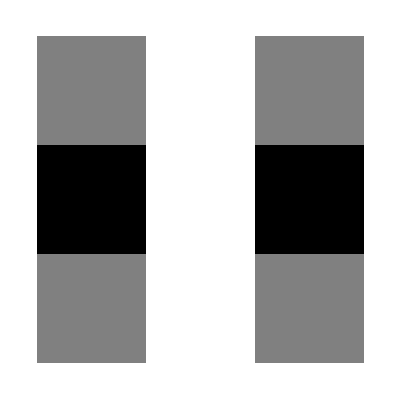
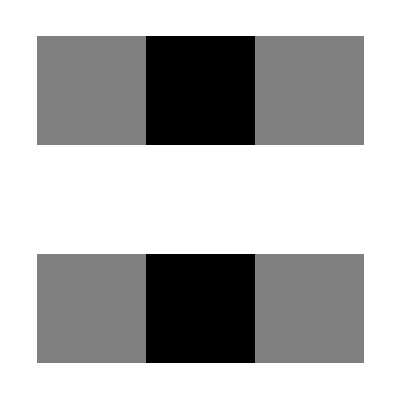
-Graphics--Graphics-Impulse reponse for the Sobel filters in the x and y directions

```mathematica
sobelX={{-1,0,1},{-2,0,2},{-1,0,1}}/4;
sobelY={{1,2,1},{0,0,0},{-1,-2,-1}}/4;
Labeled[Row[{ArrayPlot[sobelX,Frame->False],Spacer[40],ArrayPlot[sobelY,Frame->False]}],"Impulse reponse for the Sobel filters in the x and y directions",LabelStyle->captionStyle]
```

```mathematica
labelHighPassXRay="Filtering x-ray tiles with the Sobel highpass filter";
infoHighPassXRay="Sobel filtering is to a kind of edge detection filter that brings out the most important edges. This occurs because one Sobel filter is a horizontal stripe (emphasizing horizontal features) and the other Sobel filter is a vertical stripe (emphasizing vertical features). The overall method combines these two to locate string horizontal and vertical features.\n\nObserve that in most cases, inverting the image has no effect when applying the Sobel filter.";
Manipulate[
If[invert=="negative",imgXHP=allImagesXray[[i]],imgXHP=ColorNegate[allImagesXray[[i]]]];
dX=ImageConvolve[imgXHP,sobelX];dY=ImageConvolve[imgXHP,sobelY];
ImageAdjust[Image[Sqrt[ImageData[dX]^2+ImageData[dY]^2]]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoHighPassXRay]}],
FrameLabel->Style[labelHighPassXRay,Medium],TrackedSymbols->{i,invert},SaveDefinitions->saveDef]
```

This is interesting: the Sobel/gradient style filter emphasizes the boundaries in the image and suppresses (blackens out) the parts where there is little change.

```mathematica
specLine
```

-Graphics-

There are several filters built in to Mathematica that operate on this same principle, and they offer several more degrees of control over the output than is possible when operating with a single fixed set of filter weights as above.

```mathematica
labelGradientXRay="The gradient filter is another variety of highpass filter";
infoGradientXRay="This implementation of a gradient (derivative) filter gives large values (white) when the change is great and small values (black) when the change is small. The neighborhood parameter controls the size of the region over which the derivative is calculated. The brightness parameter multiplies the output by a factor in order to scale the output image for easy viewing.\n\nObserve the way the highpass filter brings out the cracks (discontinuities) in L17 (neigborhood 2 brightness 10).\n\nObserve that in most cases, inverting the image has no effect when applying the Sobel filter.";
Manipulate[If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
ImageMultiply[GradientFilter[img,r],s],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoGradientXRay]}],
{{r,1,"neighborhood"},1,10,1},
{{s,8,"brightness"},1,50},
FrameLabel->Style[labelGradientXRay,Medium],TrackedSymbols->{i,r,s,invert},SaveDefinitions->saveDef]
```

The neighborhood parameter controls the size of the filter (how many terms are used to estimate the gradient). The brightness parameter scales all the pixels of the image via multiplication. Notice how the filter emphasizes edges: in some images these outline the threads and in others such as L17_Diag05, a major visible feature is the cracks in the painting.

```mathematica
specLine
```

-Graphics-

The next demonstration shows the same filter applied to a colored image. The filter is actually applied to a grayscale version, and hence all color information is lost. The ImageApply[ ] command just inverts the pixels (like ColorNegate[]) because it is easier to look at. Such high pass or sharpening filters can highlight the brush strokes (because they form edges) in a painting.

```mathematica
labelEdgeFilter="When the gradient filter is applied to color images,\nit is actually applied to a grayscale version";
infoEdgeFilter="The gradient filter is applied to a grayscale version of a color image (and hence all color information is lost).\n\nThis can highlight brush strokes (because they form edges) in a painting. Choose any of the vanGoghBrush images (neighborhood 4-6 adjust brightness to taste).";
Manipulate[ColorNegate[ImageMultiply[GradientFilter[allImagesColor[[i]],r],s]],Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoEdgeFilter]}],
{{r,4,"neighborhood"},1,10,1},{{s,21,"brightness"},50,0.1},
FrameLabel->Style[labelEdgeFilter,Medium],TrackedSymbols->{i,r,s},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

In comparison, the LaplacianGaussianFilter[ ] follows the same kind of logic as the GradientFilter[ ], but when applied to color images it operates separately on the red, green, and blue channels. Hence the edges are enhanced while the colors may be changed significantly.

```mathematica
labelEdgeFilterColor="The LaplacianGaussianFilter[ ] is applied separately to\nthe red, green and blue channels";
infoEdgeFilterColor="Operating separately on the red, green, and blue channels means that edges are found in each channel separately before being recombined into the output image.\n\nLarger neighborhoods highllight larger and bolder structures in the image. Example: in the bedroom with neighborhood of 1 there are thousands of small lines and features. With a neighborhood of 7, only the major features (such as chairs, windows, bed) are outlined.";
Manipulate[ImageMultiply[LaplacianGaussianFilter[allImagesColor[[i]],r],s],Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoEdgeFilterColor]}],
{{r,3,"neighborhood"},1,10,1},{{s,23,"brightness"},0.1,50},FrameLabel->Style[labelEdgeFilterColor,Medium],TrackedSymbols->{i,r,s},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

And there are a number of built-in filters. They are put together in this demonstration using a kind of symbolic substitution: “filtertype” is a variable that takes on any of the values specified in the Manipulate[ ] function, i.e., any of {Blur, Sharpen, MeanFilter, GaussianFilter, MedianFilter, MinFilter, CommonestFilter}. This variable then becomes the function that is used when applied to [img,radius].

```mathematica
labelBuiltInFilters="Mathematica has a number of built-in filter types";
infoBuiltInFilters="Demonstration of a variety of built-in filter types shows how simple and powerful the symbolic substitution can be (in this case, the symbol filterType takes on a function name from the list and is applied directly to the image).\n\nSharpen brings out the edges (while leaving colors intact).\n\nBlur, MeanFilter, and Gaussian filter smear the image much like the BoxMatrix and DiskMatrix.\n\nMinFilter, MedianFilter, and CommonestFilter operate nonlinearly, combining pixel values in the neighborhood according to the named rule (min, median, and most common).";
Manipulate[img=ImageResize[allImagesColor[[i]],{400}];
filterType[img,radius],{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},{filterType,{Sharpen,Blur,MeanFilter,GaussianFilter,MedianFilter,MinFilter,CommonestFilter}},
Row[{Control[{{radius,20},1,30,1}],Spacer[20],info[infoBuiltInFilters]}],
FrameLabel->Style[labelBuiltInFilters,Medium],TrackedSymbols->{i,filterType,radius},SaveDefinitions->saveDef]
```

```mathematica
labelBandpassFilters="The bandpass filter allows specification of the pass-band";
infoBandpassFilters="Demonstration of the bandpass filter. For higher frequencies, it is common to binarize the output to emphasize the edges.";
Manipulate[img=ImageResize[allImagesColor[[i]],{700}];
imDisp=ImageAdjust[BandpassFilter[img,{wfreq,wfreq+0.1},radius]];
Which[bin=="True",MorphologicalBinarize[imDisp],bin=="False",imDisp,bin=="Product",ImageMultiply[img,MorphologicalBinarize[imDisp]]],Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],Control[{{bin,"False","Binarize"},{"False","True","Product"}}]}],Row[{Control[{{wfreq,0,"frequency"},0,1}],Spacer[20],Control[{{radius,20},1,30,1}],Spacer[20],info[infoBandpassFilters]}],FrameLabel->Style[labelBandpassFilters,Medium],TrackedSymbols->{i,wfreq,bin,radius},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Notice what a nice job the Sharpen filter does in bringing out the cracks in the canvas.

```mathematica
labelSharpen="The sharpen filter does a nice job emphasizing the cracks in the canvas";
infoSharpen="Like the highpass filter above, the sharpen can be used to emphasize edges such as the cracks in L17.\n\nOperating on the positive x-ray L17 (increase the radius), it can suppress the cracks.\n\nShown are the image (left) the sharpened image (middle) and the difference between the image and its sharpened version.\n\nThis also shows how the sharpening works: add the output of a high pass filter to the originl image.";
Manipulate[If[invert=="negative",imgS=allImagesXray[[i]],imgS=ColorNegate[allImagesXray[[i]]]];finalImg=Sharpen[imgS,sharpenRadius];
Grid[{{Image[imgS,ImageSize->{300}],Image[finalImg,ImageSize->{300}],Image[ImageAdjust[ImageSubtract[imgS,finalImg]],ImageSize->{300}]}}],Row[{Control[{{i,cracks,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],Control[{{sharpenRadius,4.5,"sharpen radius"},0.1,15,Appearance->"Labeled"}],Spacer[10],info[infoSharpen]}],
FrameLabel->Style[labelSharpen,Medium],TrackedSymbols->{i,sharpenRadius,invert},SaveDefinitions->saveDef]
```